### Uniform MC Samples

```mathematica
samples = Table[RandomVariate[UniformDistribution[{-1, +1}]], {i, 1, 1000}];
```

```mathematica
Mean[samples]
Variance[samples]
```

-0.0225124

0.337076

### Basis and Dual Basis

```mathematica
eps[z_] := 0.9 * LegendreP[0, z] + 0.05 LegendreP[1, z]
pdf[b_, c_, z_] :=  LegendreP[0, z]/2 + b  LegendreP[1, z] + c  LegendreP[2, z]
f[j_, z_]:=LegendreP[j,z]
fTilde[j_,z_]:=(2j+1)/2f[j,z]
Table[Integrate[f[i, z] fTilde[j, z], {z, -1, +1}], {i, 0, 4}, {j, 0, 4}];
MatrixForm[%]
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
Integrate[pdf[b,c,z],{z,-1,1}]
```

1

```mathematica
ClearAll[truePDF]
truePDF[z_] := pdf[0.01, 0.07, z]
```

### Integrals

```mathematica
integralMC[i_, j_] := Sum[fTilde[i, samples[[n]]] f[j, samples[[n]]] eps[samples[[n]]] , {n, 1, Length[samples]}] *2 / Length[samples]
```

```mathematica
integral[i_, j_] := Integrate[fTilde[i, z] f[j, z] eps[z], {z, -1, +1}]
Table[Integrate[fTilde[i, z] f[j, z], {z, -1, +1}], {i, 1, 3}, {j, 1, 3}];
MatrixForm[%]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

### Matrix Mij

```mathematica
matMC = ParallelTable[integralMC[i, j], {i, 0, 5}, {j, 0, 5}];
MatrixForm[%]
```

(0.898874 | -0.00339885 | 0.00508548 | 0.00787429 | 0.00427487 | 0.00241972
-0.0101965 | 0.909045 | 0.0100951 | 0.0138668 | 0.0145319 | -0.00170333
0.0254274 | 0.0168252 | 0.917132 | 0.0118903 | 0.00235467 | 0.0174485
0.05512 | 0.0323559 | 0.0166465 | 0.898701 | 0.0123439 | -0.00937022
0.0384738 | 0.0435957 | 0.00423841 | 0.0158708 | 0.883809 | 0.0214099
0.0266169 | -0.00624556 | 0.0383867 | -0.0147246 | 0.0261677 | 0.907532)

```mathematica
mat = Table[integral[i, j], {i, 0, 5}, {j, 0, 5}];
MatrixForm[%]
```

(0.9 | 0.0166667 | 0. | 0. | 1.11022×10^-16 | -6.93889×10^-18
0.05 | 0.9 | 0.02 | 0. | -1.38778×10^-17 | -4.44089×10^-16
0. | 0.0333333 | 0.9 | 0.0214286 | 0. | 0.
5.55112×10^-17 | 8.88178×10^-16 | 0.03 | 0.9 | 0.0222222 | 3.55271×10^-15
0. | 0. | -2.66454×10^-15 | 0.0285714 | 0.9 | 0.0227273
0. | 1.77636×10^-15 | -2.22045×10^-16 | 7.10543×10^-15 | 0.0277778 | 0.9)

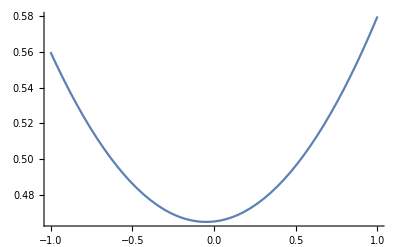

```mathematica
Plot[truePDF[z], {z, -1, +1}]
```

### Efficiency - Corrected Estimates of Observables

```mathematica
vecS = Table[Integrate[fTilde[i, z] truePDF[z] eps[z] , {z, -1, +1}], {i, 0, 5}]
```

{0.450167,0.0354,0.0633333,0.0021,5.55112×10^-16,9.71445×10^-17}

```mathematica
Inverse[mat].vecS
vecScorrected =  %/ ({2, 0, 0, 0, 0, 0}.Inverse[mat].vecS)
vecScorrected
```

{0.5,0.01,0.07,-1.32013×10^-18,8.22042×10^-16,8.0099×10^-17}

{0.5,0.01,0.07,-1.32013×10^-18,8.22042×10^-16,8.0099×10^-17}

{0.5,0.01,0.07,-1.32013×10^-18,8.22042×10^-16,8.0099×10^-17}

```mathematica
Inverse[mat].{2, 0, 0, 0, 0, 0}
```

{2.22451,-0.123686,0.0045846,-0.00015294,4.85903×10^-6,-1.4997×10^-7}

```mathematica
Table[Integrate[f[i, z], {z, -1, +1}], {i, 0, 4}]
```

{2,0,0,0,0}

```mathematica
vecSMC = Table[Sum[fTilde[i, samples[[n]]] truePDF[samples[[n]]] eps[samples[[n]]], {n, 1, Length[samples]}], {i, 0, 5}] * 2/ Length[samples]
```

{0.449759,0.00469884,0.0770812,0.0290488,0.0199696,0.015933}

```mathematica
covSMC = ParallelTable[Sum[(vecSMC[[i + 1]] - fTilde[i, samples[[n]]] truePDF[samples[[n]]] eps[samples[[n]]])(vecSMC[[j + 1]] - fTilde[j, samples[[n]]] truePDF[samples[[n]]] eps[samples[[n]]]),  {n, 1, Length[samples]}] * 2 / Length[samples] / (Length[samples] - 1), {i, 0, 5}, {j, 0, 5}]
```

{{0.000101855,9.89486×10^-6,0.0000327903,8.49994×10^-6,6.04132×10^-6,4.22137×10^-6},{9.89486×10^-6,0.000344915,0.0000307182,0.0000670776,0.0000203277,-1.51718×10^-7},{0.0000327903,0.0000307182,0.000564751,0.0000474139,0.0000805494,0.0000292018},{8.49994×10^-6,0.0000670776,0.0000474139,0.000769841,0.0000625691,0.0000893683},{6.04132×10^-6,0.0000203277,0.0000805494,0.0000625691,0.000972453,0.0000890227},{4.22137×10^-6,-1.51718×10^-7,0.0000292018,0.0000893683,0.0000890227,0.0012123}}

```mathematica
MatrixForm[covSMC]
Sqrt[Diagonal[covSMC]]
```

(0.000101855 | 9.89486×10^-6 | 0.0000327903 | 8.49994×10^-6 | 6.04132×10^-6 | 4.22137×10^-6
9.89486×10^-6 | 0.000344915 | 0.0000307182 | 0.0000670776 | 0.0000203277 | -1.51718×10^-7
0.0000327903 | 0.0000307182 | 0.000564751 | 0.0000474139 | 0.0000805494 | 0.0000292018
8.49994×10^-6 | 0.0000670776 | 0.0000474139 | 0.000769841 | 0.0000625691 | 0.0000893683
6.04132×10^-6 | 0.0000203277 | 0.0000805494 | 0.0000625691 | 0.000972453 | 0.0000890227
4.22137×10^-6 | -1.51718×10^-7 | 0.0000292018 | 0.0000893683 | 0.0000890227 | 0.0012123)

{0.0100923,0.0185719,0.0237645,0.027746,0.0311842,0.0348181}

```mathematica
Inverse[matMC].vecSMC
vecSMCcorrected =  %/ ({2, 0, 0, 0, 0, 0}.Inverse[matMC].vecSMC)
vecSMCcorrected
```

{0.5,0.01,0.07,-7.85776×10^-17,1.02078×10^-16,-5.20417×10^-17}

{0.5,0.01,0.07,-7.85776×10^-17,1.02078×10^-16,-5.20417×10^-17}

{0.5,0.01,0.07,-7.85776×10^-17,1.02078×10^-16,-5.20417×10^-17}